```mathematica
Assuming[{RH>0},Series[Exp[-(√((RH)^2+x^2+2(RH) x cosTh)-(RH-H))/h],{x,0,1}]]
Integrate[%,{x,-p,d-p}]//Simplify
```

ⅇ^(-H/h)-(cosTh ⅇ^(-H/h) x)/h+O[x]^2

(d ⅇ^(-H/h) (-cosTh d+2 h+2 cosTh p))/(2 h)

```mathematica
1-(-cosTh d+2 h+2 cosTh p)/(2 h)//Simplify
```

(cosTh (d-2 p))/(2 h)

```mathematica
Assuming[{RH>0},Series[Exp[-(√((RH)^2+x^2+2(RH) x cosTh)-(RH-H))/h],{RH,∞,1}]]
Integrate[%,{x,-p,d-p}]//Simplify
```

ⅇ^((-H-cosTh x)/h)+((-1+cosTh^2) ⅇ^(-H/h-(cosTh x)/h) x^2)/(2 h RH)+O[1/RH]^2

1/(2 cosTh^3 RH)ⅇ^(-(cosTh d+H-cosTh p)/h) (-2 (-1+ⅇ^((cosTh d)/h)) h^2+2 cosTh h (d+(-1+ⅇ^((cosTh d)/h)) p)-2 cosTh^3 h (d+(-1+ⅇ^((cosTh d)/h)) p)+cosTh^4 (-(d-p)^2+ⅇ^((cosTh d)/h) p^2)+cosTh^2 (d^2-2 d p+(-1+ⅇ^((cosTh d)/h)) (-p^2+2 h (h+RH))))

```mathematica
Integrate[2π Sin[x],{x,0,π}]
Integrate[2π Sin[x] 3/4(1+Cos[x]^2),{x,0,π}]
4π//N
NIntegrate[2π Sin[x] (3(1-g^2)(1+Cos[x]^2))/(2(2+g^2)(1+g^2-2g Cos[x])^(3/2))/.g->0.1,{x,0,π}]
Integrate[2π Sin[x](1.12+0.4Cos[x]),{x,0,π}]
```

4 π

4 π

12.5664

12.5664

14.0743

```mathematica
P[θ_]:=3/(16π)(1+Cos[θ]^2)
Integrate[2π Sin[x] P[x]P[π-x],{x,0,π}]*4π
```

21/20

```mathematica
P[θ_]:=1/(4π)
Integrate[2π Sin[x] P[x]P[π-x],{x,0,π}]*4π
```

1

```mathematica
P[θ_]:=(3(1-g^2)(1+Cos[x]^2))/(8π(2+g^2)(1+g^2-2g Cos[x])^(3/2))/.g->0.95
Integrate[2π Sin[x] P[x]P[π-x],{x,0,π}]*4π
```

213.248

```mathematica
Integrate[2π Sin[x] Cos[x] 1/π,{x,0,π/2}]
```

1

6.75

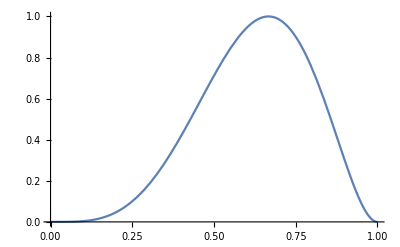

```mathematica
1/FindMaxValue[x^2(1-x),x]
Plot[(6.75 x^2(1-x))^2,{x,0,1},PlotRange->Full]
```

```mathematica
Rationalize[0.14814814814814817]
```

4/27

```mathematica
Sum[q^n,{n,0,5}]-(q^6-1)/(q-1)//Simplify
```

0

```mathematica
{.3,.3,.3}
```

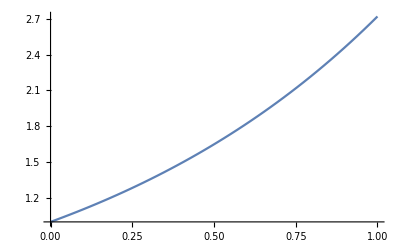

```mathematica
Plot[Exp[x],{x,0,1}]
```

```mathematica
Manipulate[Plot[x^q(1-x)^(1-q),{x,0,1}],{q,0,1}]
```

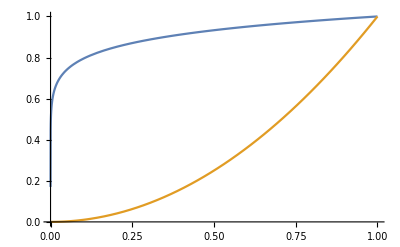

```mathematica
Plot[{x^(.1),x^2},{x,0,1}]
```

```mathematica
Solve[(q^n-1)/(q-1)==D,q]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[(-1+q^n)/(-1+q)==D,q]